## todo: ramp up retro, monte carlo to figure out where the atom goes?

```mathematica
Clear[λtrap,β,ϕ];
(*periodicity*)
FullSimplify[Abs[Exp[I (2π)/λtrap z]+β  Exp[-I (2π)/λtrap z]]^2]
FullSimplify[(ⅇ^((4 ⅈ π z)/λtrap)+β)(ⅇ^(-(4 ⅈ π z)/λtrap+I ϕ)+β)]
```

ⅇ^(4 π Im[z/λtrap]) Abs[ⅇ^((4 ⅈ π z)/λtrap)+β]^2

(ⅇ^((4 ⅈ π z)/λtrap)+β) (ⅇ^(-(4 ⅈ π z)/λtrap+ⅈ ϕ)+β)

period:(2 z)/λtrap
lattice part:1+β^2+2 β Cos[(4 π z)/λtrap]

## add gaussian profile, perfectly aligned foci with variable back reflection or make the retro beam less focused shift back refl in the z and r directions and see change in contrast.

## expand about minima; ignore the linear term

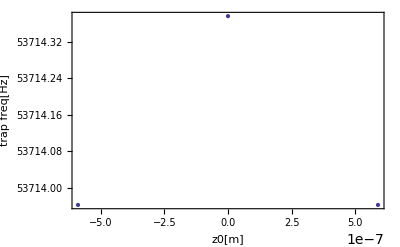

{-0.828067}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

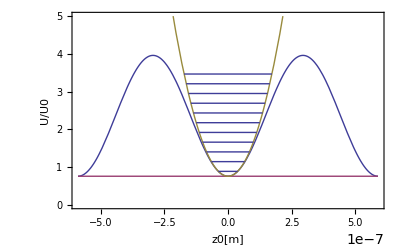

```mathematica
Clear["Global`*"]
(*units and constants for trap depth mostly*)
kHz=10^3;
nm=10^-9;
mK=10^-3;
uK=10^-6;
us=10^-6;
um=10^-6;
kB=1.38064852 10^-23;
ℏ=1.0545718 10^-34;
amu=1.66054 10^-27;
λtrap=1178 nm;
m=132.90545 amu;

nmax=1; (*how many lattice sites should I plot*)
U0=kB 0.01mK; (*depth of bare tweezer (no retro)*)
w0=7.5um;

zR=(π w0^2)/λtrap;
w=w0√(1+((λtrap z)/(π w0^2))^2);

frad=3.2kHz;
T=10 uK;
Δr=√((kB T)/(m (2π frad)^2));
r=0;2Δr; (*sub different r to check broadening due to temperature in the radial direciton*)

β=Sqrt[0.64]; (*ratio of retro ELECTRIC FIELD to forward ELECTRIC FIELD?? (due to misalignment or poor focussing. approximately equivalent to expanding waist by a factor of 1/α (and keeping same total power; see below)*)
z0=(λtrap n)/2;
trapfreqs=
Reap[
Do[
d=U0 (w0/w Exp[-r^2/w^2])^2(1+β^2+2 β Cos[(4 π z)/λtrap]);
a=Normal[Series[d,{z,z0,2}]];
dEnv=(1+β)^2 U0 (w0/w Exp[-r^2/w^2])^2;

Sow[{n,z0,f/.Solve[1/2 m(2π f)^2==-Coefficient[a,z^2],f][[2]]}];

,{n,-nmax,nmax}]
][[2,1]];

Clear[n];
(*
nn is the harmonic oscillator level,
n.,nnn is the lattice site.
*)
nnn=0;
levels=Reap[
Do[
Sow[4-(dEnv-(nn+1/2)2π ℏ Cases[trapfreqs,x_/;x[[1]]==nnn][[1,3]])/U0/.z->z0/.n->nnn]
,
{nn,0,10}]
][[2,1]];

ListPlot[trapfreqs[[;;,{2,3}]],Axes->False,Frame->True,FrameLabel->{"z0[m]","trap freq[Hz]","trap freq vs n[lattice site]"}]
(*difference of the transitio freqs of
 adjacent sites. forgetting about vertical offset*)
Differences[Differences[trapfreqs[[;;,3]]]]

plotranges=(z/.Solve[4-(dEnv-1/2 m (2π Cases[trapfreqs,x_/;x[[1]]==nnn][[1,3]])^2(z-z0)^2)/U0==#/.n->nnn,z]&/@levels)[[;;,{1,4}]];

levelsPlot=
Thread[{levels,
Join[{z},#]&/@
plotranges
}];

Show[Join[
{
Plot[{
4-d/U0,
4-dEnv/U0,

4-(dEnv-1/2 m (2π Cases[trapfreqs,x_/;x[[1]]==nnn][[1,3]])^2(z-z0)^2)/U0/.n->nnn
},{z,z0/.n->-nmax,z0/.n->nmax},Axes->False,Frame->True,FrameLabel->{"z0[m]","U/U0"},
PlotRange->{All,{0,5}}]
,
Plot@@@levelsPlot
}]
]
```

## actually want shallow contrast because otherwise the broadening due to the radial temperature completely washes out levels. (if trap is tighter overall, the radial dimension broadens levels in the z dir. )

## to shift phase of retro, just do 1+β^2+2 β Cos[(4 π z)/λtrap+ϕ] and add correspondingly scaled shift to the z part of the envelope do mc simulation of atom when you adiabatically ramp up the lattice

# showing the validity of the approximation

if the returning light is defocused by w0→α w0, and β=1/α, then the 2nd eqn is a pretty good approx of the 1st for our starting tempereature. (ie assume same gaussian envelope of the retro but attenuate the amplitude)
1-Abs[(w0/w[w0]Exp[-r^2/w[w0]^2])Exp[I (2π)/λtrap z]+(w0/w[α w0]Exp[-r^2/w[α w0]^2]) Exp[-I (2π)/λtrap z]]^2 ~
,
1-(w0/w[w0]Exp[-r^2/w[w0]^2])^2(1+β^2+2 β Cos[(4 π z)/λtrap])

```mathematica
Clear[w,λtrap,α,β,r]
λtrap=970nm;
α=1/β;
β=.8;
w[w0_]:=w0√(1+((λtrap z)/(π w0^2))^2);
Plot3D[{
1-Abs[(w0/w[w0] Exp[-r^2/w[w0]^2])Exp[I (2π)/λtrap z]+(β w0/w[w0] Exp[-r^2/w[w0]^2]) Exp[-I (2π)/λtrap z]]^2 (*attenuate retro ELECTRIC field by β*)
,

1-Abs[(w0/w[w0] Exp[-r^2/w[w0]^2])Exp[I (2π)/λtrap z]+(w0/w[α w0] Exp[-r^2/w[α w0]^2]) Exp[-I (2π)/λtrap z]]^2 (*expand retro by α*)
,

1-(w0/w[w0] Exp[-r^2/w[w0]^2])^2(1+β^2+2 β Cos[(4 π z)/λtrap]) (*approx expression*)

},{r,-100nm,100nm},{z,-1um,1um},PlotRange->{All,All,{-3,1}},AxesLabel->{"r","z"}]

(*error*)
Plot3D[{

Abs[(w0/w[w0] Exp[-r^2/w[w0]^2])Exp[I (2π)/λtrap z]+(w0/w[α w0] Exp[-r^2/w[α w0]^2]) Exp[-I (2π)/λtrap z]]^2

-(w0/w[w0] Exp[-r^2/w[w0]^2])^2(1+β^2+2 β Cos[(4 π z)/λtrap])

},{r,-100nm,100 nm},{z,-1um,1um},PlotRange->{All,All,{-3,1}},AxesLabel->{"r","z"}]
```

-Graphics3D-

-Graphics3D-

# vary the retro power

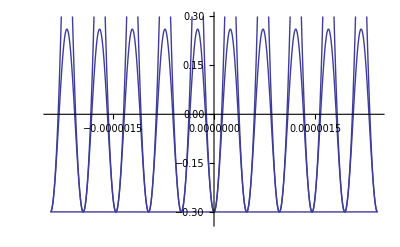

```mathematica
nmax=5; (*how many lattice sites to view*)
Clear[w,λtrap,α,β,r,z0]
U0=kB 0.67mK; (*use real number to get trap freqs*)
U0=1; (*use 1 to get ratio of lattice depth to bare tweezer depth*) 
λtrap=970nm;
z0=(λtrap n)/2;
α=1/β;
β=.14;
w[w0_]:=w0√(1+((λtrap z)/(π w0^2))^2);
a=U0(1-(w0/w[w0] Exp[-r^2/w[w0]^2])^2(1+β^2+2 β Cos[(4 π z)/λtrap])); (*actual potential*)
b=U0(1-(w0/w[w0] Exp[-r^2/w[w0]^2])^2(1+β)^2); (*envelope*)

rr=100nm;
Normal[Series[a,{z,z0,2}]]/.n->#/.r->rr&/@Range[-nmax,nmax];

Plot[Join[{
a/.r->rr,
b/.r->rr},%],
{z,-z0/.n->nmax,z0/.n->nmax},PlotRange->{All,{U0 1.1(1-(1+β)^2),U0(-1+(1+β)^2)}}]
```

```mathematica
ns=Range[0,nmax]; (*which lattice sites to calculate for*)
c=Normal[Series[a,{z,z0,2}]]/.n->#/.r->0&/@ns;(*fit parabola at each lattice site*)
Coefficient[#,z^2]&/@c;
trapfreqs=Flatten[Solve[√(1/2 m)2π f==√Coefficient[#,z^2]]&/@c];

trapfreqs=Thread[{ns,%}]
```

{{0,f→2.32242×10^18},{1,f→2.32242×10^18},{2,f→2.32239×10^18},{3,f→2.32235×10^18},{4,f→2.32229×10^18},{5,f→2.32222×10^18}}

## approx all trap freqs in different lattice sites as the same (~12% worse near edges) approx the trap freq at different r the same (~2%, worse near centre) 200kHz at β = 0.2--- 20kHz, 4kHz 500kHz at β = 1 ---- 50kHz, 10kHz gradient (in the middle) goes:

```mathematica
b/(2π ℏ)/10^6/.z->z0/.r->0/.n->#&/@ns

ListPlot[Thread[{ns,%}],Joined->True,PlotLabel->"offset [MHz] vs lattice site"]
ListPlot[Thread[{ns[[2;;]],Differences[%%]}],Joined->True,PlotLabel->"Δoffset [MHz] vs lattice site"]
```

{-4.52153×10^26,-4.52139×10^26,-4.52098×10^26,-4.52028×10^26,-4.51931×10^26,-4.51806×10^26}

-Graphics-

-Graphics-